```mathematica
(*Define the zero to power zero to be 1*)
Unprotect[Power];
Power[0|0.,0|0.]=1;
Protect[Power];

(*Definition of coefficients A(m,j)*)
A[n_,k_]:=0
A[n_,k_]:=(2 k+1)*Binomial[2 k,k]*Sum[A[n,j]*Binomial[j,2 k+1]*(-1)^(j-1)/(j-k)*BernoulliB[2 j-2 k],{j,2 k+1,n}]/;2 k+1≤n
A[n_,k_]:=(2 n+1)*Binomial[2 n,n]/;k==n;

(*Definition of coefficients U[a=1,l,m,t]*)
U[a_,l_,m_,t_]:=(-1)^m Sum[Sum[Binomial[j,t] A[m,j] k^(2 j-t) (-1)^j,{j,t,m}],{k,a,l}];

(*Max Alekseyev's revision on U[a,l,m,t]*)
UBernouli[k_,t_,m_]:=Sum[Binomial[j,t]*A[m,j]*(-1)^j/(2 j-t+1)*Binomial[2 j-t+1,k]*BernoulliB[2 j-t+1-k],{j,t,m}];

(*Definition of the RIGHT part of polynomial Pm(l,T)*)
a=1;
PR[a_,l_,m_,T_]:=Sum[(-1)^(m-k)*U[a,l,m,k]*T^k,{k,0,m}];

(*Definition of the LEFT part of polynomial^{a,l} Pm(T)*)
P[a_,l_,m_,T_]:=Sum[Sum[A[m,j]*k^j*(T-k)^j,{j,0,m}],{k,a,l}];

(*Definition of the polynomial g_m(k,T)*)
g[m_,k_,T_]:=Sum[A[m,j]*k^j*(T-k)^j,{j,0,m}];
```

```mathematica
(*Print the list of RIGHT polynomials in T,taken over m,it verifies odd-power identity*)
Table[Simplify[PR[a,T,m,T]],{m,0,12}]
```

{T,T^3,T^5,T^7,T^9,T^11,T^13,T^15,T^17,T^19,T^21,T^23,T^25}

```mathematica
(*Print the list of LEFT polynomials in T,taken over m,it verifies odd-power identity*)
Table[Simplify[P[a,T,m,T]],{m,0,12}]
```

{T,T^3,T^5,T^7,T^9,T^11,T^13,T^15,T^17,T^19,T^21,T^23,T^25}

```mathematica
(*Print the list of U coefficients within certain limit of summation*)
m=2;Column[Table[U[1,l,m,t],{l,1,10},{t,0,m}]]
```

{31,60,30}
{512,540,150}
{2943,2160,420}
{10624,6000,900}
{29375,13500,1650}
{68256,26460,2730}
{140287,47040,4200}
{263168,77760,6120}
{459999,121500,8550}
{760000,181500,11550}

1-120 (2-k) k+630 (2-k)^4 k^4

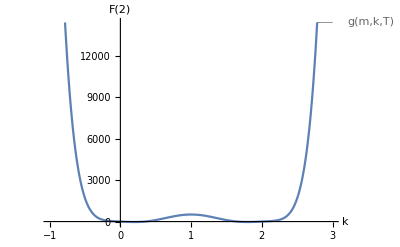

```mathematica
(*Plot of LEFT polynomials given fixed T over k (symmetry verification)*)
m=4;
s=-1;
T=2;
g[m,k,T]
Plot[g[m,k,T],{k,s,T-s},PlotLabels->"Expressions",AxesLabel->{Automatic,F[T]}]
```

```mathematica
(*Print the triangle with values of g_m(k,T) with shifting by's'*)
Column[Table[g[m=2,k,T],{T,0,10},{k,-1,T+1}],Center]
```

{31,1,31}
{121,1,1,121}
{271,1,31,1,271}
{481,1,121,121,1,481}
{751,1,271,481,271,1,751}
{1081,1,481,1081,1081,481,1,1081}
{1471,1,751,1921,2431,1921,751,1,1471}
{1921,1,1081,3001,4321,4321,3001,1081,1,1921}
{2431,1,1471,4321,6751,7681,6751,4321,1471,1,2431}
{3001,1,1921,5881,9721,12001,12001,9721,5881,1921,1,3001}
{3631,1,2431,7681,13231,17281,18751,17281,13231,7681,2431,1,3631}

```mathematica
(*The values of polynomial g_m(k,T) for fixed'm','T' over k*)
ROWgm[a_,m_,k_,T_]:=Table[g[m,k,T],{k,a,T-a}]
Column[Table[ROWgm[a=0,m=1,k,T],{T,0,10}],Left]
```

{1}
{1,1}
{1,7,1}
{1,13,13,1}
{1,19,25,19,1}
{1,25,37,37,25,1}
{1,31,49,55,49,31,1}
{1,37,61,73,73,61,37,1}
{1,43,73,91,97,91,73,43,1}
{1,49,85,109,121,121,109,85,49,1}
{1,55,97,127,145,151,145,127,97,55,1}

```mathematica
(*T-th generated by ROWgm[a_,m_,k_,T_] row triangle*)
Column[Table[ROWgm[a=-s,m=2,k,0],{s,0,5}],Center]
```

{1}
{31,1,31}
{481,31,1,31,481}
{2431,481,31,1,31,481,2431}
{7681,2431,481,31,1,31,481,2431,7681}
{18751,7681,2431,481,31,1,31,481,2431,7681,18751}

```mathematica
(*Print of the certain column k of triangle g_m(T,k)*)
COLUMNgm[m_,k_,T_,a_]:=Table[g[m,k,T],{T,k,a}]
COLUMNgm[m=1,k=4,T,a=20]
```

{1,25,49,73,97,121,145,169,193,217,241,265,289,313,337,361,385}

```mathematica
(*Partial Sum of the column of triangle g_m(T,k) k over T*)
COLUMNSUMgm[m_,k_]:=Table[Sum[g[m,k,T],{T,k,a}],{a,k,20}]
COLUMNSUMgm[1,2]
```

{1,14,39,76,125,186,259,344,441,550,671,804,949,1106,1275,1456,1649,1854,2071}

```mathematica
(*Row Sums of A[m,j]*)
RowSumAmj[m_]:=Sum[A[m,j],{j,0,m}]
Table[RowSumAmj[j],{j,0,10}]
```

{1,7,31,127,511,2047,8191,32767,131071,524287,2097151}

```mathematica
(*Row Sums of ABS(A[m,j])*)
AbsRowSumAmj[m_]:=Sum[Abs[A[m,j]],{j,0,m}]
Table[AbsRowSumAmj[j],{j,0,10}]
```

{1,7,31,155,751,4819,51871,1052995,31318591,1182921875,54074508511}

```mathematica
(*Column Sums of A[m,j]*)
ColumnSumAmj[j_]:=Sum[A[m,j],{m,0,5}]
ColumnSumAmj[2]
```

690

```mathematica
(*Integral property*)
ClearAll[m,T,l];
IntegralAmm[m_,T_]:=Integrate[A[m,m]*k^m*(T-k)^m,{k,0,T}]
Table[IntegralAmm[m=2,T],{T,0,10}]
```

```mathematica
(*Print the closed forms of LEFT polynomial*)
Column[Table[P[a=1,l,m,T],{m,0,3}],Left]
```

l
-3 l^2-2 l^3+3 l T+3 l^2 T
10 l^3+15 l^4+6 l^5-15 l^2 T-30 l^3 T-15 l^4 T+5 l T^2+15 l^2 T^2+10 l^3 T^2
7 l^2+28 l^3-70 l^5-70 l^6-20 l^7-7 l T-42 l^2 T+175 l^4 T+210 l^5 T+70 l^6 T+14 l T^2-140 l^3 T^2-210 l^4 T^2-84 l^5 T^2+35 l^2 T^3+70 l^3 T^3+35 l^4 T^3

```mathematica
(*Print the list of RIGHT polynomials,depending on summation bounds//Closed forms of RIGHT POLYNOMIALS*)
Column[Table[Expand[PR[a=1,L,m,T]],{m,0,3}],Left]
```

L
-3 L^2-2 L^3+3 L T+3 L^2 T
10 L^3+15 L^4+6 L^5-15 L^2 T-30 L^3 T-15 L^4 T+5 L T^2+15 L^2 T^2+10 L^3 T^2
7 L^2+28 L^3-70 L^5-70 L^6-20 L^7-7 L T-42 L^2 T+175 L^4 T+210 L^5 T+70 L^6 T+14 L T^2-140 L^3 T^2-210 L^4 T^2-84 L^5 T^2+35 L^2 T^3+70 L^3 T^3+35 L^4 T^3

```mathematica
(*Print out the RIGHT polynomials with fixed L and running T*)
ClearAll[T,L]
Column[Table[Expand[PR[a=1,L,m=2,T]],{T,1,5}]]
```

5 L-10 L^3+6 L^5
20 L+30 L^2-10 L^3-15 L^4+6 L^5
45 L+90 L^2+10 L^3-30 L^4+6 L^5
80 L+180 L^2+50 L^3-45 L^4+6 L^5
125 L+300 L^2+110 L^3-60 L^4+6 L^5

```mathematica
(*Print out the RIGHT polynomials with fixed T and running L*)
Column[Table[Expand[PR[a=1,L,m=2,T]],{L,1,5}]]
```

31-60 T+30 T^2
512-540 T+150 T^2
2943-2160 T+420 T^2
10624-6000 T+900 T^2
29375-13500 T+1650 T^2

```mathematica
(*Upside-down triangle of UBernoulli numbers,see definition above*)
m=4;Column[Table[UBernouli[k,j,m],{j,0,m},{k,1,2 m-j+1}],Center]
```

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-2].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-3].

General::stop: Further output of BernoulliB::intnm will be suppressed during this calculation.

{0,-60,180,0,-294,0,420,-315,70}
{-60,270,0,-735,0,1470,-1260,315}
{90,0,-630,0,1890,-1890,540}
{0,-210,0,1050,-1260,420}
{-21,0,210,-315,126}

```mathematica
(*Verification of the odd power identity with UBernoulli numbers*)
OddPowerIdentity[T_,m_]:=Sum[Sum[(-1)^(2 m-j)*UBernouli[k,j,m]*T^(k+j),{k,1,2 m-j+1}],{j,0,m}]
Table[OddPowerIdentity[S,m],{m,0,10}]
```

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-2].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

General::stop: Further output of BernoulliB::intnm will be suppressed during this calculation.

{S,S^3,S^5,S^7,S^9,S^11,S^13,S^15,S^17,S^19,S^21}

```mathematica
(*UBernouli identity terms*)R=2;
Table[Sum[(-1)^(2 m-j)*UBernouli[k,j,m]*R^(k+j),{k,1,2 m-j+1}],{m,0,7},{j,0,m}]
```

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-2].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

General::stop: Further output of BernoulliB::intnm will be suppressed during this calculation.

{{2},{-4,12},{32,-120,120},{-124,812,-1680,1120},{752,-5280,15120,-20160,10080},{-724,22308,-108240,221760,-221760,88704},{51872,-259896,792792,-1921920,2882880,-2306304,768768},{950036,-2505348,-1638000,13933920,-28828800,34594560,-23063040,6589440}}

```mathematica
(*UBernouli identity terms is's'*)
OddPowerIdentityTerms[T_,m_]:=Column[Table[Sum[(-1)^(2 m-j)*UBernouli[k,j,m]*T^(k+j),{k,1,2 m-j+1}],{j,0,m}],Left]
OddPowerIdentityTerms[S,3]
```

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-1].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-2].

BernoulliB::intnm: Non-negative machine-sized integer expected at position 1 in BernoulliB[-3].

General::stop: Further output of BernoulliB::intnm will be suppressed during this calculation.

-7 S^2+28 S^3-70 S^5+70 S^6-20 S^7
7 S^2-42 S^3+175 S^5-210 S^6+70 S^7
14 S^3-140 S^5+210 S^6-84 S^7
35 S^5-70 S^6+35 S^7

```mathematica
(*Definition of F[s,n,k]*)
F[s_,n_,k_]:=k*Sum[Binomial[j,s-2],{j,0,n-k-1}]
```

```mathematica
(*Fifth power by means of Faulhaber's formula, with binomial ciefficients replaced by F[s,n,k]*)
Sum[120*F[4,n+1,k]+30*F[2,n,k]+1,{k,1,n}]
```

n^5

```mathematica
(*Triangle generated by LEFT polynomials with fixed'T' and running'm'*)
T=3;
Table[Sum[A[m,j]*k^j (T-k)^j,{k,1,T}],{m,0,10},{j,0,m}]
```

{{3},{3,24},{3,0,240},{3,-56,0,2240},{3,-480,0,0,20160},{3,-5544,5280,0,0,177408},{3,-87360,144144,0,0,0,1537536},{3,-1800216,3931200,-960960,0,0,0,13178880},{3,-47523840,124048320,-59404800,0,0,0,0,112020480},{3,-1579155816,4655851200,-3142557440,282172800,0,0,0,0,945950720},{3,-64690211520,208026170352,-173818444800,32996853120,0,0,0,0,0,7945986048}}

```mathematica
(*Triangle generated by RIGHT polynomials with fixed'T' and running'm'*)
T=3;
Table[(-1)^(m-k)*U[1,T,m,k]*T^k,{m,0,10},{k,0,m}]
```

{{3},{-81,108},{2943,-6480,3780},{-110961,347508,-370440,136080},{4297023,-17511120,27011880,-18779040,5000940},{-166441041,839582172,-1700871480,1733387040,-891392040,185912496},{6434953983,-38749327344,97419470148,-131000950080,99505846440,-40561256736,6952857912},{-246968598321,1732184564868,-5210413954200,8717576147280,-8767547989200,5305538478240,-1791105235920,260750936160},{9437164816383,-75530391166080,264624544568160,-530132696009280,664355935643400,-533519232966720,268286968469520,-77309274968640,9787110753420},{-357854832558801,3223425161283228,-12902731202884320,30131070803847360,-45248713115762520,45326036952836640,-30294630665339040,13033112691044160,-3276933686306280,367219056101040},{13550790332018943,-135405487328428944,609261254941786524,-1625083922030627520,2845274544473213160,-3416914884897049536,2850673336071921360,-1631737330302119040,613466270973115560,-136847683255963680,13763121482486376}}